# MKID - Response Matrix plots

## Setup

Loads upstream notebooks and points Direc to ../../input/MKID.

```mathematica
nbDir = NotebookDirectory[];
Direc = FileNameJoin[{ParentDirectory[ParentDirectory[nbDir]], "input", "MKID"}];
Get[FileNameJoin[{nbDir, "08_response_matrix.nb"}]];
SetDirectory[Direc];
Print["Direc = ", Direc];
```

## Response function

### Matrix data

#### Plotting

```mathematica
(*TES*)
(* Use imported data *)
```

```mathematica
binsAl10={{0.1,0.2},{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.0},{1.0,1.1}};
binsAl={{0.1,0.3},{0.3,0.5},{0.5,0.7},{0.7,0.9},{0.9,1.1}};
```

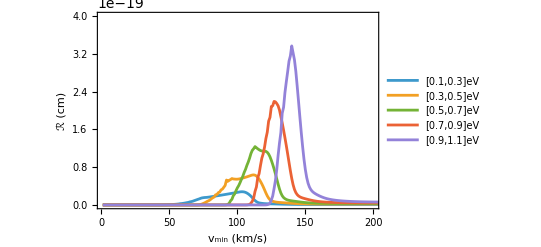

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"curlyRTES/Al_R5_q0M1_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["TES: m=10 MeV", 16]}},
PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
3.3 10^-19*cm
```

1.66667×10^-14

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_10MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_10MeV_q=0_5bins.pdf

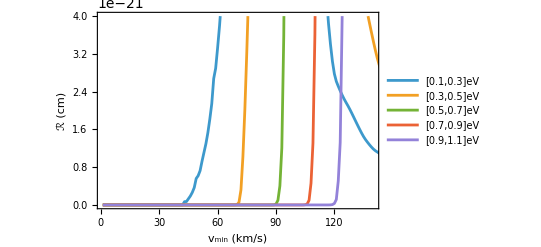

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,140},{0,4 10^-21}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_10MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_10MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M1.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"},PlotLegends->{"[0.1, 0.2]eV","[0.2, 0.3]eV","[0.3, 0.4]eV","[0.4, 0.5]eV","[0.5, 0.6]eV","[0.6, 0.7]eV","[0.7, 0.8]eV","[0.8, 0.9]eV","[0.9, 1.0]eV","[1.0, 1.1]eV",LegendLayout->{"Column",2}}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M1.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)},PlotLegends→{[0.1, 0.2]eV,[0.2, 0.3]eV,[0.3, 0.4]eV,[0.4, 0.5]eV,[0.5, 0.6]eV,[0.6, 0.7]eV,[0.7, 0.8]eV,[0.8, 0.9]eV,[0.9, 1.0]eV,[1.0, 1.1]eV,LegendLayout→{Column,2}}]

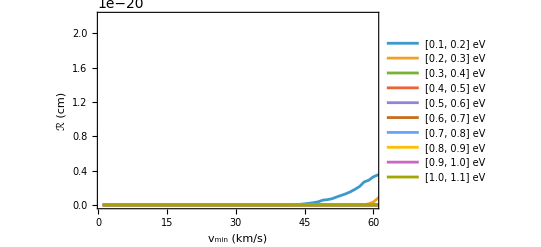

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_10MeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,60},{0,2.2 10^-20}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_10MeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][10 MeV][1,800]
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M1_Ko.csv"],vals]
```

{4.94967×10^-44,9.8234×10^-44,1.42832×10^-43,1.86592×10^-43,2.25044×10^-43}

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M1_Ko.csv

```mathematica
Alexp
```

1.84056×10^49

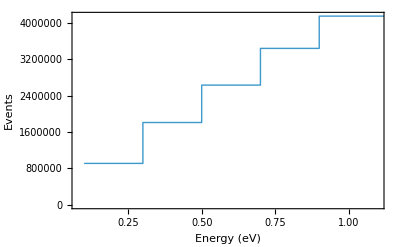

```mathematica
stepData1=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
ListStepPlot[stepData1,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
etaList = Table[
ηth[10 MeV][vm kps][238 kps,250 kps, 544 kps]*cm,{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaHaloM1_Ko.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaHaloM1_Ko.csv

```mathematica
etaList = Table[
ηth[1000 MeV][vm kps][238 kps,250 kps, 544 kps]*cm + ηtb[1000 MeV][vm kps][2.16 kps, 11.2 kps] * cm,{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaBoundM3_Ko.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaBoundM3_Ko.csv

```mathematica
etaList = Table[
(0.75ηth[10 MeV][vm kps][238 kps,250 kps, 544 kps]*cm+0.25ηtd[10 MeV][vm kps][70 kps,100 kps, 714 kps] * cm),{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaDiskM1_Ko_25percent.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaDiskM1_Ko_25percent.csv

```mathematica
etaList = Table[
(0.95ηth[10 MeV][vm kps][238 kps,250 kps, 544 kps]*cm+0.05ηtd[10 MeV][vm kps][70 kps,100 kps, 714 kps] * cm),{vm, 1 , 800 }];
Export[FileNameJoin[Direc,"Eta/EtaDiskM1_Ko_5percent.csv"],etaList]
```

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaDiskM1_Ko_5percent.csv

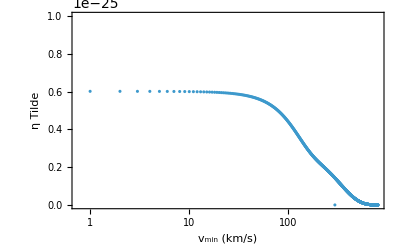

```mathematica
ListPlot[etaList,
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{0, 10^-25}}, 
ScalingFunctions->{"Log","Linear"}]
```

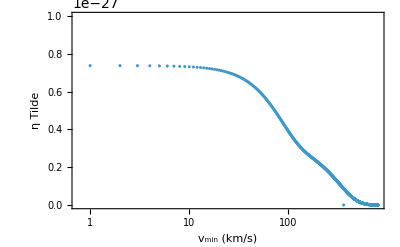

```mathematica
ListPlot[etaList,
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{0, 10^-27}}, 
ScalingFunctions->{"Log","Linear"}]
```

```mathematica
Export[FileNameJoin[Direc,"Eta/EtaDiskM3_Ko.csv"],etaList]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Eta/EtaDiskM3_Ko.csv

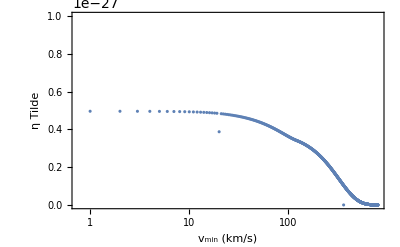

```mathematica
ListPlot[Table[
9/10(ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps]*cm+1/9 ηtd[1000 MeV][vm kps][230 kps,50 kps, 70 kps] * cm),{vm, 1 , 800 }],
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{0, 10^-27}}, 
ScalingFunctions->{"Log","Linear"}]
```

```mathematica
Alexp
```

1.84056×10^49

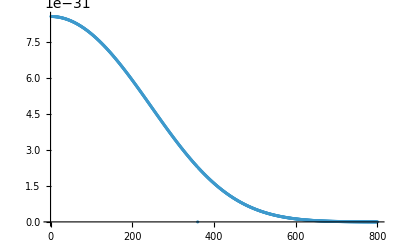

```mathematica
ListPlot[Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }]]
```

```mathematica
Export[FileNameJoin[Direc,"etaTilde_M1.h5"],Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }]]
Export[FileNameJoin[Direc,"etaTilde_M1.csv"],Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }]]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/etaTilde_M1.h5

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/etaTilde_M1.csv

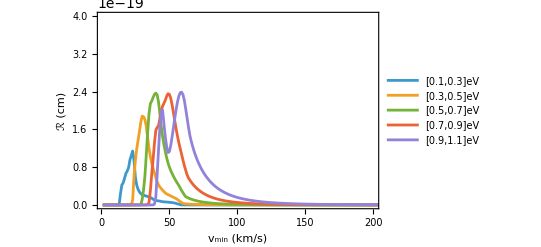

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"curlyRTES/Al_R5_q0M2_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["TES: m=100 MeV", 16]}},
PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_100MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_100MeV_q=0_5bins.pdf

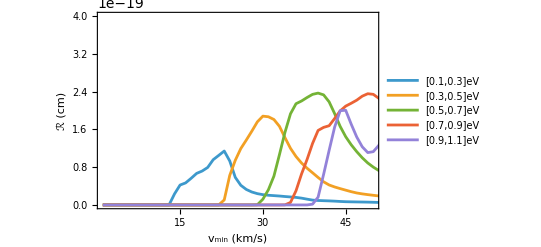

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_100MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_100MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M2.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M2.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)}]

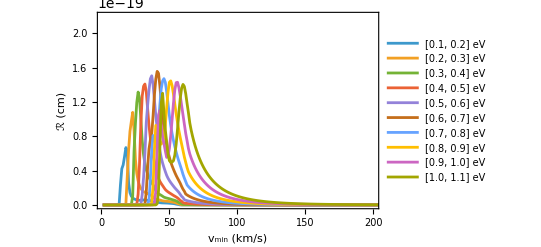

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

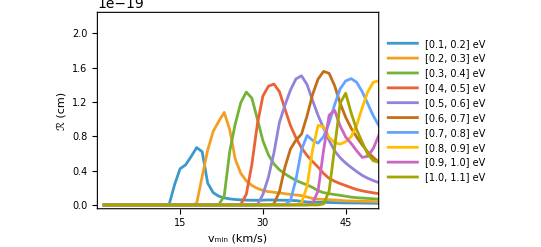

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.26,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

```mathematica
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf",%319,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][100 MeV][1,800]
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M2_Ko.csv"],vals]
```

{5.67545×10^-45,1.17057×10^-44,1.74225×10^-44,2.29674×10^-44,2.83939×10^-44}

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M2_Ko.csv

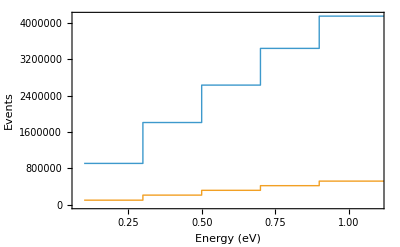

```mathematica
stepData2=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
ListStepPlot[{stepData1,stepData2},PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

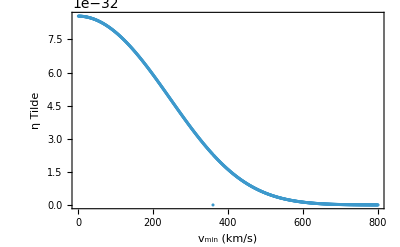

```mathematica
ListPlot[Table[ηth[100 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

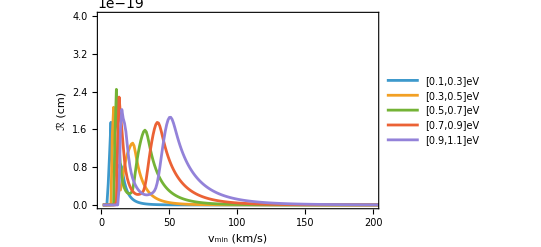

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"curlyRTES/Al_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["TES: m=1 GeV", 16]}},
PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

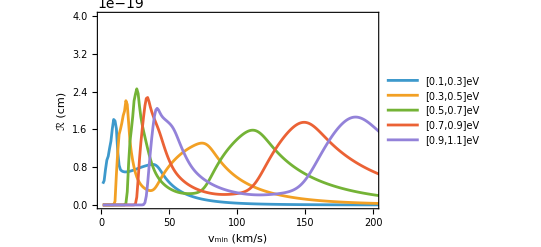

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_1GeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_1GeV_q=0_5bins.pdf

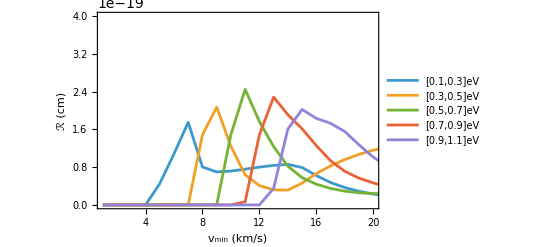

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,20},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M3.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M3.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)}]

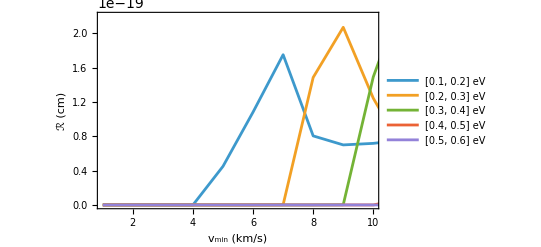

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,10},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.27,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

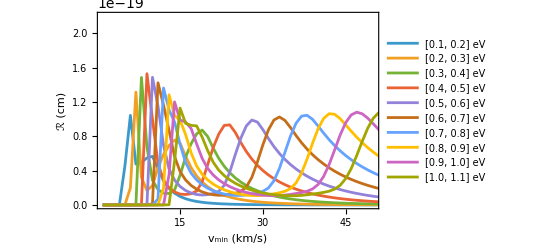

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.72,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
ηtilde[5]
```

ηtilde[5]

```mathematica
RvminAl5custom[CRlistAl  * Alexp, ηtilde][100 MeV][200][5, 0.51758]
```

{81561.4,164915.,245018.,328154.,405539.}

```mathematica
vals = RvminAl5custom[CRlistAl, ηtilde][1000 MeV][200][5,108];
```

Part::pkspec1: The expression 2.93207 cannot be used as a part specification.

Part::pkspec1: The expression 4.86414 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][1000 MeV][1,800]
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M3_Ko.csv"],vals]
```

{5.74109×10^-46,1.15497×10^-45,1.74196×10^-45,2.30029×10^-45,2.84975×10^-45}

/Users/koichiromacstudio/Library/CloudStorage/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M3_Ko.csv

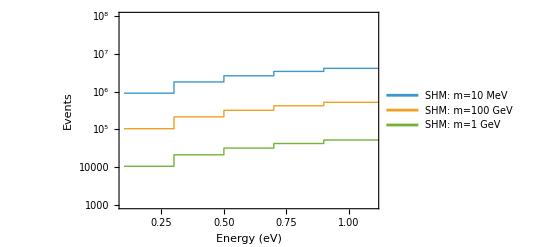

```mathematica
stepData3=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
EventsSHM = ListStepPlot[{stepData1, stepData2, stepData3},PlotStyle->Thick,Frame->True,
FrameLabel->{{"Events", None}, {"Energy (eV)","TES events for 8200 ng・month"}},
PlotRange->{{0.1,1.1},{10^3,10^8}},
PlotLegends->Placed[LineLegend[{"SHM: m=10 MeV","SHM: m=100 GeV","SHM: m=1 GeV"},LegendLayout->{"Column",1}, LabelStyle->Directive[8]],Scaled[{0.15,0.85}]],
ScalingFunctions->"Log"]
```

```mathematica
kps
```

3.32323×10^-6

```mathematica
Export[FileNameJoin[Direc,"results/Events/Events_TES_SHM_q=0_5bins.pdf"],EventsSHM,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/Events/Events_TES_SHM_q=0_5bins.pdf

```mathematica
ListPlot[Table[ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

```mathematica
(*MKID*)
(* Use imported data *)
```

```mathematica
binsTiN10={{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.0},{1.0,1.1}};
binsTiN={{0.2,0.3},{0.3,0.5},{0.5,0.7},{0.7,0.9},{0.9,1.1}};
```

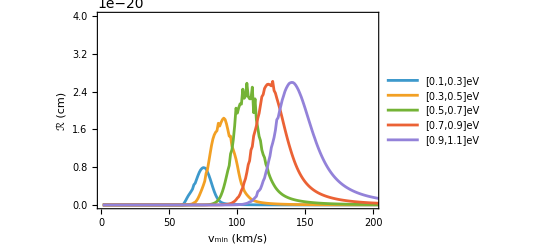

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M1_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistTiN/cm,PlotRange->{{1,200},{0,4 10^-20}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["MKID: m=10 MeV", 16]}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_MKID_10MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_MKID_10MeV_q=0_5bins.pdf

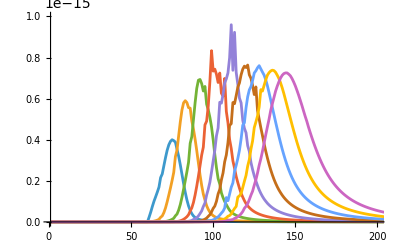

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M1.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

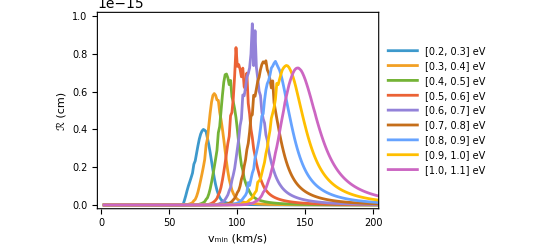

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_10MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",1}, LabelStyle->Directive[8]],Scaled[{0.15,0.52}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_10MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][10 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M1.csv"],vals]
```

{1.70213×10^-50,2.55884×10^-50,3.22273×10^-50,3.97149×10^-50,4.67044×10^-50,5.15322×10^-50,5.68153×10^-50,6.18928×10^-50,6.61773×10^-50}

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/TiN_Events10_q0M1.csv

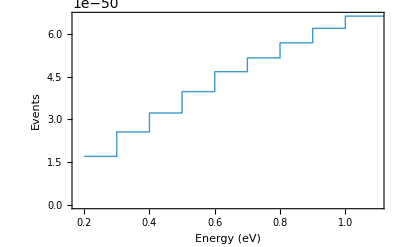

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

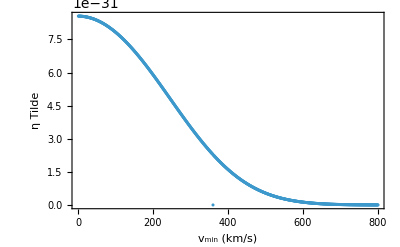

```mathematica
ListPlot[Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

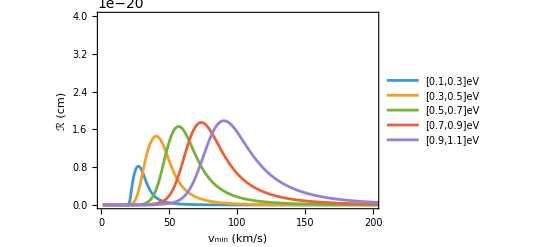

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M2_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistTiN/cm,PlotRange->{{1,200},{0,4 10^-20}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["MKID: m=100 MeV", 16]}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_MKID_100MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_MKID_100MeV_q=0_5bins.pdf

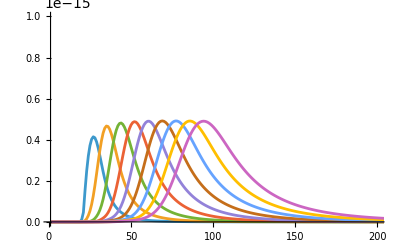

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M2.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

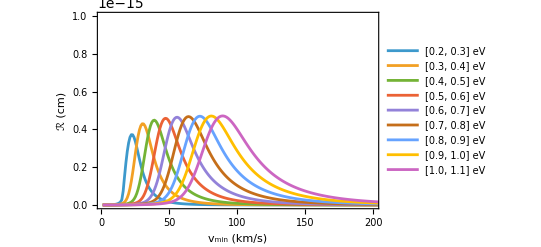

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_100MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_100MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][100 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M2.csv"],vals]
```

{1.64989×10^-51,2.53733×10^-51,3.23167×10^-51,3.90337×10^-51,4.54904×10^-51,5.16518×10^-51,5.74863×10^-51,6.29662×10^-51,6.80691×10^-51}

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/TiN_Events10_q0M2.csv

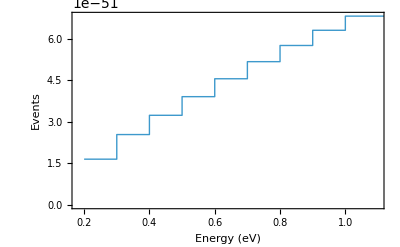

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
ListPlot[Table[ηth[100 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

-Graphics-

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M3_Ko_refined.h5"],{"Datasets","Dataset1"}];
```

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M3_Ko_refined.h5"],{"Datasets","Dataset1"}];
```

```mathematica
etaList = Table[
ηth[1000 MeV][(5+ (i - 1)0.51758) kps][230 kps,240 kps, 600 kps]*cm + ηtb[1000 MeV][(5 + (i - 1)0.51758) kps][2.441876042996079 kps, 11.2 kps] * cm,{i, 1, 200 }];
```

```mathematica
CRlistAl.etaList * Alexp
```

{1.32726×10^18,8.18033×10^15,1.69766×10^13,2.66828×10^9,3.24616×10^9}

```mathematica
Export[FileNameJoin[Direc,"Al_Events5_q0M3_exposure.csv"],CRlistAl.etaList * Alexp]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_Events5_q0M3_exposure.csv

```mathematica
etaList = Table[
ηth[1000 MeV][(6 + (i - 1)0.51256) kps][230 kps,240 kps, 600 kps]*cm + ηtb[1000 MeV][(6 + (i - 1)0.51256) kps][2.441876042996079 kps, 11.2 kps] * cm,{i, 1, 200 }];
```

```mathematica
CRlistTiN.etaList * TiNexp
```

{8.07251×10^13,9.34623×10^12,4.6719×10^10,3.95002×10^9,3.38977×10^9}

```mathematica
Export[FileNameJoin[Direc,"TiN_Events5_q0M3_exposure.csv"],CRlistTiN.etaList * TiNexp]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/TiN_Events5_q0M3_exposure.csv

```mathematica
RvminTiN5custom[CRlistTiN, ηtilde][1000 MeV][200][6, 0.51256]
```

{8.63544×10^-47,2.89575×10^-46,4.19181×10^-46,5.04992×10^-46,5.0265×10^-46}

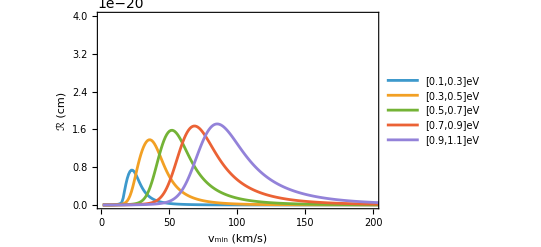

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistTiN/cm,PlotRange->{{1,200},{0,4 10^-20}},Frame->True,FrameLabel->{{Style["ℛ (cm)", 16], None}, {Style["\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)", 16],Style["MKID: m=1 GeV", 16]}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_MKID_1GeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_MKID_1GeV_q=0_5bins.pdf

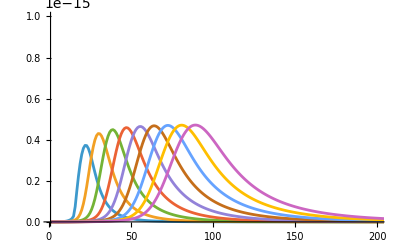

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M3.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_1GeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

-Graphics-

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_1GeV_q=0_SHM.pdf

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][1000 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M3.csv"],vals]
```

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
ListPlot[Table[ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```